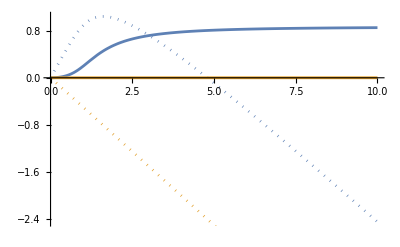

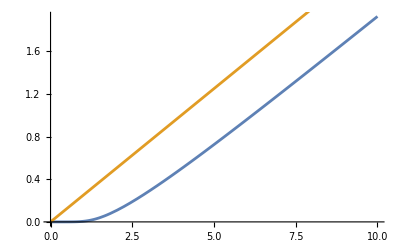

```mathematica
blue=RGBColor[0.368,0.507,0.710];
orange =RGBColor[0.881,0.611,0.142];

k2 := 1
m := 1
L := 1

(*Define the time-dependent coefficients*)
T[t_]:=  1+L^2/t^2
Tinv[t_]:= 1/T[t]
gam[t_]:= -4*(L^2/t^3)*Tinv[t]

Tmax := 10
f[y_]:= NIntegrate[-(Tinv[t]*k2+(1-T[t])*m^2-I*m*T[t]*gam[t])/(T[t]*(gam[t]-2*I*m)),{t, 0, y}]
f1 := ReImPlot[f[x],{x,0,Tmax}, PlotStyle->blue]
f2 := ReImPlot[-I*(k2/(2m))*t, {t, 0, Tmax}, PlotStyle->orange]
Show[{f1, f2}]

delta[y_]:= NIntegrate[1/(T[t]^2*(gam[t]^2+4*m^2)),{t, 0, y}]
p1 := Plot[delta[x],{x,0,Tmax}, PlotStyle->blue]
p2 := Plot[x/(4*m^2),{x,0,Tmax}, PlotStyle->orange]
Show[{p1, p2}]
```